```mathematica
(*collaborate: Qin Liu (just modified the number in canvas example)*)
```

```mathematica
pivot[iStar_,jStar_,m_]:=(
mm=m;
numRows=Dimensions[m][[1]];
numCols=Dimensions[m][[2]];
mm[[1,jStar]]=m[[iStar,numCols]];
mm[[iStar,numCols]]=m[[1,jStar]];
(* Changed counter vars i and j to ii and jj to allow i and j to be used as tableau names *)
For[ii=2,ii≤numRows,ii++,
For[jj=1,jj<numCols,jj++,
{
If[ii==iStar&&jj==jStar,mm[[ii,jj]]=1/m[[iStar,jStar]]],(* p -> 1/p *)
If[ii==iStar&&jj≠jStar,mm[[ii,jj]]=-m[[ii,jj]]/m[[iStar,jStar]]],(* q -> -q/p *)
If[ii≠iStar&&jj==jStar,mm[[ii,jj]]=m[[ii,jj]]/m[[iStar,jStar]]],(* r -> r/p *)
If[ii≠iStar&&jj≠jStar,mm[[ii,jj]]=m[[ii,jj]]-m[[iStar,jj]]*m[[ii,jStar]]/m[[iStar,jStar]]](* s -> s-qr/p *)
}
]
];
Return[mm]
)
```

```mathematica
Clear[x,y]
g1[x_,y_]=4x+3y; 
g2[x_,y_]=4x+3y; 
g3[x_,y_]=-3x+y; 
g4[x_,y_]=3x-y; 
(* define constraint constants *)
b1= 48;
b2=24;
b3=6;
b4=6;
(* define slack var functions to compute slack at any given point (x,y) *)
ss1[x_,y_]=b1-g1[x,y] ;
ss2[x_,y_]=g2[x,y]-b2;
ss3[x_,y_]=b3-g3[x,y];
ss4[x_,y_]=b4-g4[x,y];
(* define objective function *)
zz[x_,y_]=-2x-4y+4;

g1[x_]=y/.Solve[g1[x,y]==b1,{y}][[1,1]];
g2[x_]=y/.Solve[g2[x,y]==b2,{y}][[1,1]];
g3[x_]=y/.Solve[g3[x,y]==b3,{y}][[1,1]];
g4[x_]=y/.Solve[g4[x,y]==b4,{y}][[1,1]];
```

```mathematica
a==ss1[0,0]
```

{{x1,x2,x3,x4,1,},{-4,4,-3,3,48,s1},{4,-4,3,-3,-24,s2},{3,-3,-1,1,6,s3},{-3,3,1,-1,6,s4},{-2,2,-4,4,4,z}}==48

```mathematica
Clear[x,y]
```

```mathematica
Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-10,10},AspectRatio->Automatic,PlotRange->{-10,30}]
```

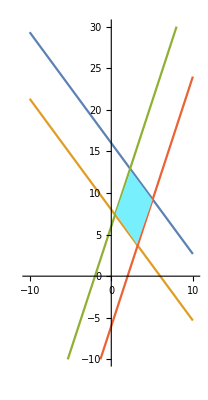

```mathematica
m0={"x1","x2","x3","x4",1,""};
m1={-4,4,-3,3,48,"s1"};
m2={4,-4,3,-3,-24,"s2"};
m3={3,-3,-1,1,6,"s3"};
m4={-3,3,1,-1,6,"s4"};
mobj={-2,2,-4,4,4,"z"};

a={m0,m1,m2,m3,m4,mobj};
Print["a = ",MatrixForm[a]]
```

a = (x1 | x2 | x3 | x4 | 1 | 
-4 | 4 | -3 | 3 | 48 | s1
4 | -4 | 3 | -3 | -24 | s2
3 | -3 | -1 | 1 | 6 | s3
-3 | 3 | 1 | -1 | 6 | s4
-2 | 2 | -4 | 4 | 4 | z)

```mathematica
(* basic solution *)
x1=0;x2=0;x3=0;x4=0;
s1=48;s2=-24;s3=6;
s4=6;z=4;
xx=x1-x2;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 0  y = 0

True

True

True

«2 more identical outputs»

```mathematica
b=pivot[4,1,a];
Print["b = ",MatrixForm[b]]
```

b = (s3 | x2 | x3 | x4 | 1 | 
-4/3 | 0 | -13/3 | 13/3 | 56 | s1
4/3 | 0 | 13/3 | -13/3 | -32 | s2
1/3 | 1 | 1/3 | -1/3 | -2 | x1
-1 | 0 | 0 | 0 | 12 | s4
-2/3 | 0 | -14/3 | 14/3 | 8 | z)

```mathematica
(* basic solution *)
x1=-2;x2=0;x3=-13/3;x4=13/3;
s1=56;s2=-32;s3=0;
s4=12;z=8;
xx=x1-x2;yy=x3+x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = -2  y = 0

True

True

True

«2 more identical outputs»

```mathematica
c=pivot[3,3,b];
Print["c = ",MatrixForm[c]]
```

c = (s3 | x2 | s2 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s1
-4/13 | 0 | 3/13 | 1 | 96/13 | x3
3/13 | 1 | 1/13 | 0 | 6/13 | x1
-1 | 0 | 0 | 0 | 12 | s4
10/13 | 0 | -14/13 | 0 | -344/13 | z)

```mathematica
(* basic solution *)
x1=6/13;x2=0;x3=96/13;x4=0;
s1=24;s2=0;s3=0;
s4=12;z=-334/13;
xx=x1-x4;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 6/13  y = 96/13

True

True

True

«1 more identical outputs»

False

```mathematica
d=pivot[2,3,b];
Print["d = ",MatrixForm[d]]
```

d = (s3 | x2 | s1 | x4 | 1 | 
-4/13 | 0 | -3/13 | 1 | 168/13 | x3
0 | 0 | -1 | 0 | 24 | s2
3/13 | 1 | -1/13 | 0 | 30/13 | x1
-1 | 0 | 0 | 0 | 12 | s4
10/13 | 0 | 14/13 | 0 | -680/13 | z)

```mathematica
(* basic solution *)
x1=30/13;x2=0;x3=168/13;x4=1;
s1=0;s2=24;s3=0;
s4=12; z=-680/13;
xx=x1-x2;yy=x3;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 30/13  y = 168/13

True

True

True

«2 more identical outputs»

```mathematica
e=pivot[5,1,d];
Print["e = ",MatrixForm[e]]
```

e = (s4 | x2 | s1 | x4 | 1 | 
4/13 | 0 | -3/13 | 1 | 120/13 | x3
0 | 0 | -1 | 0 | 24 | s2
-3/13 | 1 | -1/13 | 0 | 66/13 | x1
-1 | 0 | 0 | 0 | 12 | s3
-10/13 | 0 | 14/13 | 0 | -560/13 | z)

```mathematica
(* basic solution *)
x1=66/13;x2=0;x3=120/13;x4=1;
s1=0;s2=24;s3=12;
s4=0;z=-560/13;
xx=x1-x2;yy=x3;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 66/13  y = 120/13

True

True

True

«2 more identical outputs»

```mathematica
f=pivot[3,3,e];
Print["f = ",MatrixForm[f]]
```

f = (s4 | x2 | s2 | x4 | 1 | 
4/13 | 0 | 3/13 | 1 | 48/13 | x3
0 | 0 | -1 | 0 | 24 | s1
-3/13 | 1 | 1/13 | 0 | 42/13 | x1
-1 | 0 | 0 | 0 | 12 | s3
-10/13 | 0 | -14/13 | 0 | -224/13 | z)

```mathematica
(* basic solution *)
x1=42/13;x2=0;x3=48/13;x4=1;
s1=24;s2=0;s3=12;
s4=0; z=-224/13;
xx=x1-x2;yy=x3;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 42/13  y = 48/13

True

True

True

«2 more identical outputs»

```mathematica
g=pivot[2,1,f];
Print["g = ",MatrixForm[g]]
```

g = (x3 | x2 | s2 | x4 | 1 | 
13/4 | 0 | -3/4 | -13/4 | -12 | s4
0 | 0 | -1 | 0 | 24 | s1
-3/4 | 1 | 1/4 | 3/4 | 6 | x1
-13/4 | 0 | 3/4 | 13/4 | 24 | s3
-5/2 | 0 | -1/2 | 5/2 | -8 | z)

```mathematica
(* basic solution *)
x1=6;x2=0;x3=13/4;x4=-13/4;
s1=24;s2=0;s3=24;
s4=-12;z=-8;
xx=x1-x2;yy=x3+x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 6  y = 0

True

True

True

«2 more identical outputs»

```mathematica
h=pivot[2,3,g];
Print["h = ",MatrixForm[h]]
```

h = (x3 | x2 | s4 | x4 | 1 | 
13/3 | 0 | -4/3 | -13/3 | -16 | s2
-13/3 | 0 | 4/3 | 13/3 | 40 | s1
1/3 | 1 | -1/3 | -1/3 | 2 | x1
0 | 0 | -1 | 0 | 12 | s3
-14/3 | 0 | 2/3 | 14/3 | 0 | z)

```mathematica
(* basic solution *)
x1=2;x2=0;x3=13/3;x4=-13/3;
s1=40;s2=-16;s3=12;
s4=0; z=0;
xx=x1-x2;yy=x3+x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 2  y = 0

True

True

True

«2 more identical outputs»

```mathematica
i = pivot[3,3,h];
Print["i = ",MatrixForm[i]]
```

i = (x3 | x2 | s1 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s2
13/4 | 0 | 3/4 | -13/4 | -30 | s4
-3/4 | 1 | -1/4 | 3/4 | 12 | x1
-13/4 | 0 | -3/4 | 13/4 | 42 | s3
-5/2 | 0 | 1/2 | 5/2 | -20 | z)

```mathematica
x1=12;x2=0;x3=0;x4=0;
s1=0;s2=24;s3=42;
s4=-30; z=-20;
xx=x1-x2;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 12  y = 0

True

True

True

«2 more identical outputs»

```mathematica
j = pivot[4,1,i];
Print["j = ",MatrixForm[j]]
```

j = (x1 | x2 | s1 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s2
-13/3 | 13/3 | -1/3 | 0 | 22 | s4
-4/3 | 4/3 | -1/3 | 1 | 16 | x3
13/3 | -13/3 | 1/3 | 0 | -10 | s3
10/3 | -10/3 | 4/3 | 0 | -60 | z)

```mathematica
x1=0;x2=0;x3=16;x4=0;
s1=0;s2=24;s3=-10;
s4=22; z=-60;
xx=x1-x2;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 0  y = 16

True

True

True

«2 more identical outputs»

```mathematica
k = pivot[2,3,j];
Print["k = ",MatrixForm[k]]
```

k = (x1 | x2 | s2 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s1
-13/3 | 13/3 | 1/3 | 0 | 14 | s4
-4/3 | 4/3 | 1/3 | 1 | 8 | x3
13/3 | -13/3 | -1/3 | 0 | -2 | s3
10/3 | -10/3 | -4/3 | 0 | -28 | z)

```mathematica
x1=0;x2=0;x3=8;x4=0;
s1=24;s2=0;s3=-2;
s4=14; z=-28;
xx=x1-x2;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 0  y = 8

True

True

True

«2 more identical outputs»

```mathematica
l = pivot[3,3,k];
Print["l = ",MatrixForm[l]]
```

l = (x1 | x2 | s4 | x4 | 1 | 
-13 | 13 | -3 | 0 | 66 | s1
13 | -13 | 3 | 0 | -42 | s2
3 | -3 | 1 | 1 | -6 | x3
0 | 0 | -1 | 0 | 12 | s3
-14 | 14 | -4 | 0 | 28 | z)

```mathematica
x1=-13;x2=13;x3=-6;x4=0;
s1=66;s2=-42;s3=12;
s4=0; z=28;
xx=x1+x2;yy=x3-x4;
Print["x = ",xx,"  y = ",yy]
ss1[xx,yy]==s1
ss2[xx,yy]==s2
ss3[xx,yy]==s3
ss4[xx,yy]==s4
zz[xx,yy]==z
```

x = 0  y = -6

True

True

True

«2 more identical outputs»